# 2. domača naloga

## 1. naloga

a)  Definirajte funkcijo , ki sprejme naravni števili  in  in vrne matriko dimenzije , kjer se na vsakem mestu v matriki pojavi vsota indeksa stolpca in indeksa vrstice.
b) Izračunajte lastne vrednosti in lastne vektorje matrike .
c)  Narišite lastne vektorje matrike .
d) Izračunajte karakteristični polinom matrike .
e) Matriko  diagonalizirajte. Določite ustrezno diagonalno matriko , prehodno matriko  in .
f) Rešite matrično enačbo .

```mathematica
A[n_,m_] :=Table[i+j, {i,1,n},{j,1,m}]
```

```mathematica
Eigenvalues[A[3,3]]
Eigenvectors[A[3,3]]
```

{6+√42,6-√42,0}

{{-(-17-2 √42)/(23+4 √42),-(-20-3 √42)/(23+4 √42),1},{-(17-2 √42)/(-23+4 √42),-(20-3 √42)/(-23+4 √42),1},{1,-2,1}}

```mathematica
Graphics3D[Arrow[{{0,0,0},#}]&/@%]
```

-Graphics3D-

```mathematica
CharacteristicPolynomial[A[3,3],x]
```

6 x+12 x^2-x^3

```mathematica
G=DiagonalMatrix[Eigenvalues[A[3,3]]]
P=Transpose[Eigenvectors[A[3,3]]]
Inverse[P]
```

{{6+√42,0,0},{0,6-√42,0},{0,0,0}}

{{-(-17-2 √42)/(23+4 √42),-(17-2 √42)/(-23+4 √42),1},{-(-20-3 √42)/(23+4 √42),-(20-3 √42)/(-23+4 √42),-2},{1,1,1}}

{{(2-20/(-23+4 √42)+(3 √42)/(-23+4 √42))/(54/(-23+4 √42)-(7 √42)/(-23+4 √42)+54/(23+4 √42)+(7 √42)/(23+4 √42)+(22 √42)/((-23+4 √42) (23+4 √42))),(1+17/(-23+4 √42)-(2 √42)/(-23+4 √42))/(54/(-23+4 √42)-(7 √42)/(-23+4 √42)+54/(23+4 √42)+(7 √42)/(23+4 √42)+(22 √42)/((-23+4 √42) (23+4 √42))),(54/(-23+4 √42)-(7 √42)/(-23+4 √42))/(54/(-23+4 √42)-(7 √42)/(-23+4 √42)+54/(23+4 √42)+(7 √42)/(23+4 √42)+(22 √42)/((-23+4 √42) (23+4 √42)))},{(-2-20/(23+4 √42)-(3 √42)/(23+4 √42))/(54/(-23+4 √42)-(7 √42)/(-23+4 √42)+54/(23+4 √42)+(7 √42)/(23+4 √42)+(22 √42)/((-23+4 √42) (23+4 √42))),(-1+17/(23+4 √42)+(2 √42)/(23+4 √42))/(54/(-23+4 √42)-(7 √42)/(-23+4 √42)+54/(23+4 √42)+(7 √42)/(23+4 √42)+(22 √42)/((-23+4 √42) (23+4 √42))),(54/(23+4 √42)+(7 √42)/(23+4 √42))/(54/(-23+4 √42)-(7 √42)/(-23+4 √42)+54/(23+4 √42)+(7 √42)/(23+4 √42)+(22 √42)/((-23+4 √42) (23+4 √42)))},{(20/(-23+4 √42)-(3 √42)/(-23+4 √42)+20/(23+4 √42)+(3 √42)/(23+4 √42))/(54/(-23+4 √42)-(7 √42)/(-23+4 √42)+54/(23+4 √42)+(7 √42)/(23+4 √42)+(22 √42)/((-23+4 √42) (23+4 √42))),(-17/(-23+4 √42)+(2 √42)/(-23+4 √42)-17/(23+4 √42)-(2 √42)/(23+4 √42))/(54/(-23+4 √42)-(7 √42)/(-23+4 √42)+54/(23+4 √42)+(7 √42)/(23+4 √42)+(22 √42)/((-23+4 √42) (23+4 √42))),(22 √42)/((-23+4 √42) (23+4 √42) (54/(-23+4 √42)-(7 √42)/(-23+4 √42)+54/(23+4 √42)+(7 √42)/(23+4 √42)+(22 √42)/((-23+4 √42) (23+4 √42))))}}

```mathematica
X=LinearSolve[A[3,3]+P-G, IdentityMatrix[3]]
A[3,3].X+P.X==G.X+IdentityMatrix[3]//Simplify(*preverimo resitev*)
```

{{(97-21 √42)/(3 (-27+26 √42)),(3023-382 √42)/(3 (-27+26 √42) (-184+27 √42)),(28463-4467 √42)/(3 (-27+26 √42) (-184+27 √42))},{((-23+4 √42) (278+45 √42))/(132 (-27+26 √42)),(-22949+2690 √42)/(6 (-27+26 √42) (-184+27 √42)),(13966-1715 √42)/(6 (-27+26 √42) (-184+27 √42))},{(-184+27 √42)/(6 (-27+26 √42)),-(2 (64+7 √42))/(3 (-27+26 √42)),(218+15 √42)/(6 (-27+26 √42))}}

True

## 2. naloga

Imamo klančino z naklonom 30 stopinj dolžine 10m. Na dnu klančine se nahaja ravnina dolžine 10m. Na levem in desnem robu se nahaja stena (glej sliko). 
Kroglico z radijem 10cm spustimo na vrhu klanca, da se začne gibati pod vplivom gravitacije. Predpostavite lahko, da med kroglico in podlago ni trenja in 
da se zaradi kotaljenja energija ne izgublja. Ko pride kroglica na dno klanca, se giblje v vodoravni smeri z enako velikim vektorjem hitrosti (predpostavi, 
da je kot dovolj majhen, da na pride do odboja). 
Simulirajte kotaljenje kroglice po klančini in ravnini, ki se odbija od desnega roba.
Za gravitacijski pospešek vzemite g = 9.81, začetna hitrost kroglice naj bo v0 = 0.

a) Definiraj gravitacijski pospešek, naklon, dolžino klanca, začetno hitrost in radij kroglice.

```mathematica
g=9.81;
kot=Pi/6;
d=10;
v0=0;
r=0.1;
```

b) Nariši klančino, tla in obe steni.

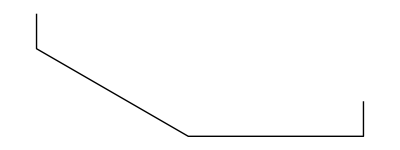

```mathematica
Graphics[Line[{{0,1},{0,-1},{Cos[kot]*d, -1-Sin[kot]*d}, {Cos[kot]*d+d, -1-Sin[kot]*d}, {Cos[kot]*d+d, 1-Sin[kot]*d}}]]
```

c) Na sliko dodaj kroglico tako, da se bo kroglica premaknila, če se spremeni njeno središče.

```mathematica
x1 = 0;
y1 = 0;
v={0,0};
t=0.1;
Graphics[{Line[{{0,1},{0,-1},{Cos[kot]*d, -1-Sin[kot]*d}, {Cos[kot]*d+d, -1-Sin[kot]*d}, {Cos[kot]*d+d, 1-Sin[kot]*d}}],
Locator[
Dynamic[{x1,y1}],
Graphics[Disk[{0,0},r],PlotRange->1]
]
}]
```

-Graphics-

d) Definiraj funkcijo `naKlancu`, ki sprejme središče kroglice in vrne `True`, če je kroglica na klancu.

```mathematica
naKlancu[{x_,y_}]:=Cos[kot]*d-r>=x;
```

```mathematica
desniRob[{x_,y_}]:=x>=18
```

e) Definiraj funkcijo `desniRob`, ki sprejme središče kroglice in vrne `True`, če je kroglica trčila ob desni rob.

f) Definiraj funkcijo `posodobiHitrost`, ki sprejme vektor trenutne hitrost kroglice in kot α ter vrne novo hitrost, gibanja po klančini z naklonom α.

```mathematica
posodobiHitrost[v_,a_]:= {v[[1]]+g*t/Tan[a],v[[2]]-g*t};
```

g) Definiraj funkcijo `hitrostNaKlanec`, ki sprejme vektor trenutne hitrosti kroglice in kot α ter vrne novo hitrost, ki jo dobi kroglica, ko iz ravnega dela preide na klanec z naklonom α.

```mathematica
hitrostNaKlanec[v_,a_]:= {v[[1]]*Cos[kot], Abs[v[[1]]*Sin[kot]]};
```

h) Definiraj funkcijo `hitrostSKlanca`, ki sprejme vektor trenutne hitrosti kroglice in vrne novo hitrost, ki jo dobi kroglica, ko s klanca preide na ravni del.

```mathematica
hitrostSKlanca[v_]:={v[[1]],0};
```

i) S pomočjo prejšnjih funkcij simuliraj premikanje kroglice.

```mathematica
x = 0.5;
y = -.8;
v={0,0};
t=0.001;
klanc = naKlancu[{x,y}];
Graphics[{Line[{{0,1},{0,-1},{Cos[kot]*d, -1-Sin[kot]*d}, {Cos[kot]*d+d, -1-Sin[kot]*d}, {Cos[kot]*d+d, 1-Sin[kot]*d}}],
Locator[
Dynamic[{x,y}],
Graphics[Disk[{0,0},r],PlotRange->1]
]
}]
While[True,
v=If[klanc,
If[naKlancu[{x,y}],posodobiHitrost[v,kot],y=-.7-Sin[kot]*d;hitrostSKlanca[v]],
If[naKlancu[{x,y}],y=-.6-Sin[kot]*d;hitrostNaKlanec[v,kot],v]
];
v=If[desniRob[{x,y}],{-v[[1]],0},v];
klanc = naKlancu[{x,y}];
x=x+v[[1]];
y=y+v[[2]];
Pause[0.1];
]
```

-Graphics-